```mathematica
Quit[];
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yuichirotada/Documents/Univ/general-tail/math

```mathematica
zetaGx[x_,mu_]=mu Sinc[x]//Simplify
```

mu Sinc[x]

```mathematica
zetabar[x_,mu_,γ_]=-1/γ Log[1-γ zetaGx[x,mu]]//Simplify
```

-Log[1-mu γ Sinc[x]]/γ

```mathematica
CompactC[x_,mu_,γ_]=2/3(1-(1+x D[zetabar[x,mu,γ], x])^2)//FullSimplify
```

2/3 (1-(1+(mu (x Cos[x]-Sin[x]))/(x-mu γ Sin[x]))^2)

```mathematica
Cp[x_,mu_,γ_]=D[CompactC[x,mu,γ], x]//Simplify;
```

```mathematica
dRdr[x_,mu_,γ_]=1+x D[zetabar[x,mu,γ], x]//Simplify
```

1+(mu (x Cos[x]-Sin[x]))/(x-mu x γ Sinc[x])

```mathematica
rmcond[x_,mu_,γ_]=-(5 x^20)/mu(D[zetabar[x,mu,γ], x]+x D[D[zetabar[x,mu,γ], x], x])//Simplify
```

-(5 x^17 (mu x^2 γ Cos[x]^2+Sin[x] (x-x^3+mu γ Sin[x])-x Cos[x] (x+2 mu γ Sin[x])+mu x γ (x Cos[x]+(-1+x^2) Sin[x]) Sinc[x]))/(-1+mu γ Sinc[x])^2

```mathematica
rmcond2[x_,mu_,γ_]=(*1/x*)(1+x D[zetabar[x,mu,γ], x])//Simplify
```

1+(mu (x Cos[x]-Sin[x]))/(x-mu x γ Sinc[x])

```mathematica
rmcond2[x,1/(2-δ),2-δ]
```

1+(x Cos[x]-Sin[x])/((2-δ) (x-x Sinc[x]))

```mathematica
Normal[Series[rmcond2[x,1/(2-δ),2-δ],{δ,0,1},{x,0,2}]]
```

x^2/20+(-1/2+x^2/40) δ

```mathematica
Solve[Normal[Series[rmcond2[x,1/(2-δ),2-δ]==0,{δ,0,1},{x,0,2}]],x]
```

{{x→-(2 √5 √δ)/(√(2+δ))},{x→(2 √5 √δ)/(√(2+δ))}}

```mathematica
x/.Solve[x/20-δ/(2x)==0,x]
```

{-√10 √δ,√10 √δ}

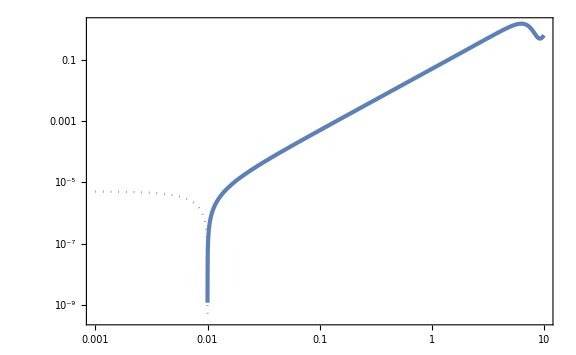

```mathematica
LogLogPlot[{rmcond2[x,1/(2-10^-5)-10^-30,2-10^-5],-rmcond2[x,1/(2-10^-5)-10^-30,2-10^-5]},{x,10^-3,10},PlotStyle->{AbsoluteThickness[3],{Color[1],Dotted}},WorkingPrecision->30]
```

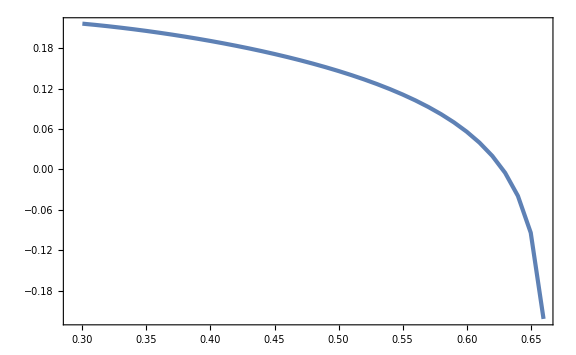

```mathematica
ListPlot[Table[{mu,FindMinimum[{rmcond2[x,mu,3/2],0<x<5},x,WorkingPrecision->30][[1]]//Quiet},{mu,3/10,1/(3/2)-10^-3,10^-2}]]
```

```mathematica
rmcondt[x_,mu_,γ_]=D[zetabar[x,mu,γ], x]+x D[D[zetabar[x,mu,γ], x], x]//Simplify
```

(mu (mu x^2 γ Cos[x]^2+Sin[x] (x-x^3+mu γ Sin[x])-x Cos[x] (x+2 mu γ Sin[x])+mu x γ (x Cos[x]+(-1+x^2) Sin[x]) Sinc[x]))/(x^3 (-1+mu γ Sinc[x])^2)

```mathematica
Normal[Series[rmcondt[ϵ,1/γ-δ,γ]==0,{δ,0,1},{ϵ,0,1}]]
```

δ (-24/ϵ^3-(11 ϵ)/350)+ϵ/(5 γ)==0

```mathematica
ϵmsol[δ_]=ϵ/.Solve[Normal[Series[rmcondt[ϵ,1/γ-δ,γ]==0,{δ,0,1},{ϵ,0,1}]],ϵ][[4]]
```

(2 √5 21^(1/4) γ^(1/4) δ^(1/4))/(70-11 γ δ)^(1/4)

```mathematica
Simplify[Normal[Series[D[Normal[Series[2zetabar[ϵ,1/γ-δ,γ],{ϵ,0,2}]], δ]/.{ϵ->ϵmsol[δ]},{δ,0,0}]]/.{γ->2},{δ>0}]
```

(√(5/3))/δ^(3/2)-1/δ+11/(14 √15 √δ)

```mathematica
rmcond2minList=Flatten[ParallelTable[{γ,mu,FindMinimum[{rmcond2[x,mu,γ],0<x<5},x,WorkingPrecision->30][[1]]//Quiet},{γ,-6,3/2,10^-2},{mu,3/10,If[γ>0,Min[11/10,1/γ-10^-3],11/10],10^-2}],1];//AbsoluteTiming
```

{1129.37,Null}

```mathematica
Export["rmcond2min.dat",rmcond2minList//N];
```

```mathematica
rmcond2minList=Import["rmcond2min.dat"];
```

```mathematica
ListContourPlot[rmcond2minList]
```

-Graphics-

```mathematica
rmcond2minint[γ_,mu_]=Interpolation[rmcond2minList][γ,mu];
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

```mathematica
mu2List=Table[{γ,mu/.FindRoot[rmcond2minint[γ,mu]==0,{mu,3/5},WorkingPrecision->30]//Quiet},{γ,-6,3/2,10^-2}];//AbsoluteTiming
```

{100.31,Null}

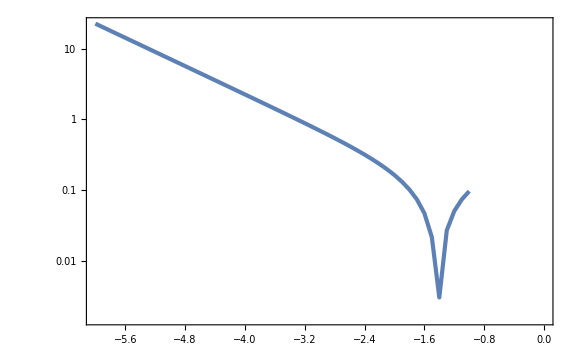

```mathematica
ListLogPlot[Table[{lndmu,Abs[FindMinimum[{rmcond2[x,1/(2-10^(-3/10))-10^lndmu,2-10^(-3/10)],0<x<5},x,WorkingPrecision->30][[1]]//Quiet]},{lndmu,-6,-1,10^-1}]]
```

```mathematica
rmcond2minListfine=Flatten[ParallelTable[{2-10^lndγ,1/(2-10^lndγ)-10^lndmu,FindMinimum[{rmcond2[x,1/(2-10^lndγ)-10^lndmu,2-10^lndγ],0<x<5},x,WorkingPrecision->30][[1]]//Quiet},{lndγ,-3,-3/10,10^-2},{lndmu,-6,-1,10^-2}],1];//AbsoluteTiming
```

{1117.75,Null}

```mathematica
Export["rmcond2minfine.dat",rmcond2minListfine//N];
```

```mathematica
rmcond2minListfine=Import["rmcond2minfine.dat"];
```

```mathematica
ListContourPlot[rmcond2minListfine]
```

$Aborted

```mathematica
rmcond2minintfine[γ_,mu_]=Interpolation[rmcond2minListfine][γ,mu];
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

```mathematica
mu2Listfine=Table[{2-10^lndγ,mu/.FindRoot[rmcond2minintfine[2-10^lndγ,mu]==0,{mu,1/3},WorkingPrecision->30]//Quiet},{lndγ,-3,-3/10,10^-2}];//AbsoluteTiming
```

{91.6655,Null}

```mathematica
Export["mu2List.dat",Join[mu2List,Sort[mu2Listfine//N]]//N];
```

```mathematica
mu2Listtot=Import["mu2List.dat"];
```

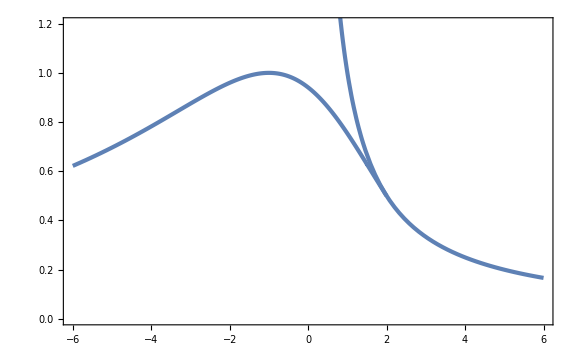

```mathematica
Show[ListPlot[mu2Listtot,PlotRange->{{-6,6},{0,1.2}}],Plot[1/x,{x,0,6}]]
```

```mathematica
mu2int[γ_]=Interpolation[mu2Listtot][γ];
```

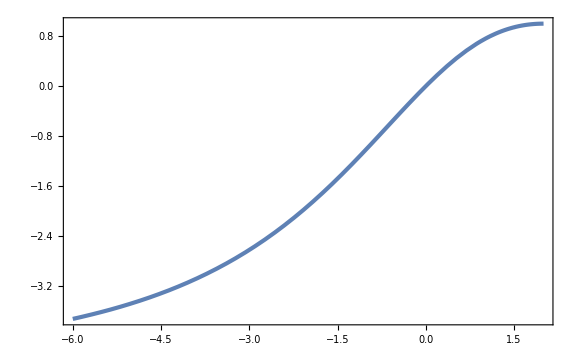

```mathematica
Plot[mu2int[γ]γ,{γ,-6,2}]
```

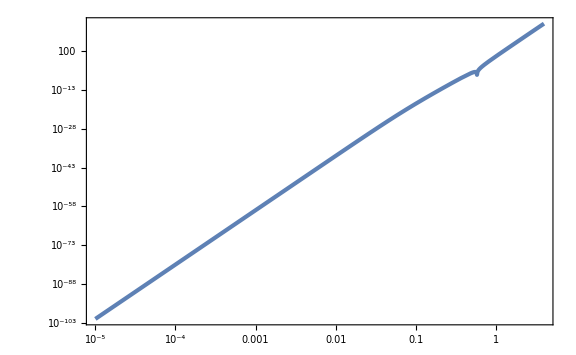

```mathematica
LogLogPlot[Abs[rmcond[x,1,1-10^-3]],{x,10^-5,4},WorkingPrecision->30]
```

```mathematica
xmList=Table[{muγ,x/.FindRoot[rmcond[x,1,muγ]==0,{x,4},WorkingPrecision->30]//Quiet},{muγ,-4,1-10^-3,10^-2}];
```

```mathematica
xm2List=Flatten[ParallelTable[{γ,mu,x/.FindRoot[rmcond2[x,mu,γ]==0,{x,1/3},WorkingPrecision->30]//Quiet},{γ,-2,(*2-10^-3*)3/2,10^-2},{mu,mu2int[γ]+10^-3,If[γ>0,Min[1.1,1/γ-10^-2],1.1](*mumaxint[γ]*),10^-2}],1];//AbsoluteTiming
```

{2.10471,Null}

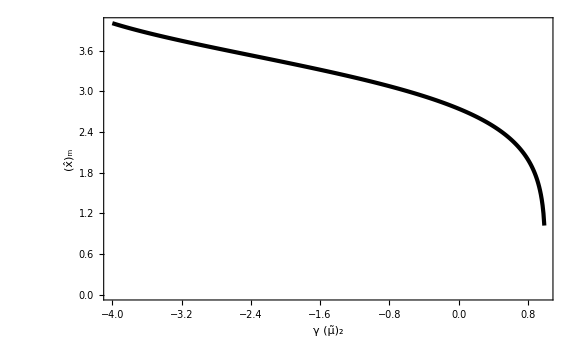

```mathematica
ListPlot[xmList,FrameLabel->{Subscript[OverTilde[μ], 2] γ,Subscript[OverHat[x], "m"]},PlotStyle->{AbsoluteThickness[3],Black}]
```

```mathematica
xmint[muγ_]=Interpolation[xmList][muγ];
xm2int[γ_,mu_]=Interpolation[xm2List][γ,mu];
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

```mathematica
Rarea[x_,mu_,γ_]=E^zetabar[x,mu,γ] x;
```

```mathematica
VMS[mu_,γ_]:=(4π)/3 Rarea[xmint[mu γ],mu,γ]^3/;mu<mu2int[γ];
VMS[mu_,γ_]:=(4π)/3 Rarea[xm2int[γ,mu],mu,γ]^3/;mu>=mu2int[γ];
```

```mathematica
Cbarm[mu_,γ_]:=1/VMS[mu,γ] 4π NIntegrate[CompactC[x,mu,γ] Rarea[x,mu,γ]^2 D[Rarea[x,mu,γ], x],{x,0,xmint[mu γ]}]/;mu<mu2int[γ]
Cbarm[mu_,γ_]:=1/VMS[mu,γ] 4π NIntegrate[CompactC[x,mu,γ] Rarea[x,mu,γ]^2 D[Rarea[x,mu,γ], x],{x,0,xm2int[γ,mu]},WorkingPrecision->30]/;mu>=mu2int[γ]
```

```mathematica
CbarmList=Flatten[ParallelTable[If[γ==0,Nothing,{γ,mu,Cbarm[mu,γ]//Quiet}],{γ,-2,6,10^-2},{mu,10^-2,If[γ>0,Min[1.1,1/γ-10^-2],1.1],10^-2}],1];//AbsoluteTiming
```

{265.35,Null}

```mathematica
Export["Cbarm.dat",CbarmList];
```

```mathematica
CbarmList=Import["Cbarm.dat"]//ToExpression;
```

```mathematica
Cbarmint[γ_,mu_]=Interpolation[CbarmList][γ,mu];
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

Interpolation::umprec: Interpolation on unstructured grids is currently only supported for machine numbers. The data will be coerced to machine precision.

```mathematica
muthList=Import["nr_threshold.txt","Data"];
```

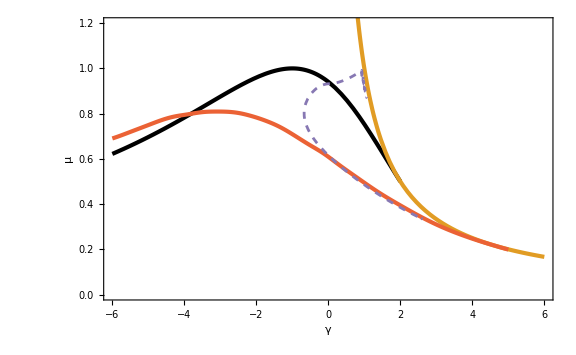

```mathematica
Show[Plot[mu2int[γ],{γ,-6,2},PlotRange->{{-6,6},{0,1.2}},PlotStyle->{Black,AbsoluteThickness[3]},FrameLabel->{γ,μ}],
Plot[1/γ,{γ,0,6},PlotStyle->{Color[2],AbsoluteThickness[3]}],
ListPlot[muthList,PlotStyle->{Color[4],AbsoluteThickness[3]}],
ContourPlot[Cbarmint[γ,mu]UnitStep[1-mu γ],{γ,-2,6},{mu,10^-2,1.1},Contours->{2/5},ContourShading->None,ContourStyle->{{Color[5],Dashed,AbsoluteThickness[2]}},MaxRecursion->3]]
```

```mathematica
muthint[γ_]=Interpolation[muthList][γ];
```

```mathematica
γmin=γ/.FindRoot[mu2int[γ]==muthint[γ],{γ,-4}]
```

-3.81559

```mathematica
alpha[mu_,γ_]=KK(mu-muthint[γ])^p/.{KK->1,p->0.36};
```

```mathematica
MoMks[mu_,γ_]=xmint[mu γ]^2 Exp[2zetabar[xmint[mu γ],mu,γ]]alpha[mu,γ];
dLogMdmu[mu_,γ_]=D[Log[MoMks[mu,γ]], mu]//Simplify;
```

```mathematica
PlotMoMks[mu_,γ_]:=MoMks[mu,γ]/;(γ<2&&mu≥muthint[γ]&&mu≤mu2int[γ])
PlotMoMks[mu_,γ_]:=None/;(γ<2&&(mu<muthint[γ]||mu>mu2int[γ]))
PlotMoMks[mu_,γ_]:=MoMks[mu,γ]/;(γ≥2&&mu≥muthint[γ]&&mu<1/γ)
PlotMoMks[mu_,γ_]:=None/;(γ≥2&&(mu<muthint[γ]||mu≥1/γ))
```

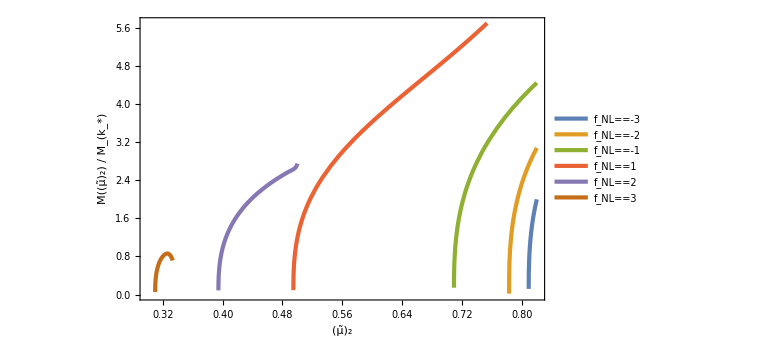

```mathematica
Plot[{PlotMoMks[mu,-3],PlotMoMks[mu,-2],PlotMoMks[mu,-1],PlotMoMks[mu,1],PlotMoMks[mu,2],PlotMoMks[mu,3]},{mu,0.3,0.82},FrameLabel->{Subscript[OverTilde[μ], 2],Row[{M[Subscript[OverTilde[μ], 2]]," / ",Subscript[M, Subscript[k, "*"]]}]},PlotLegends->Placed[LineLegend[{Subscript[f, NL]==-3,Subscript[f, NL]==-2,Subscript[f, NL]==-1,Subscript[f, NL]==1,Subscript[f, NL]==2,Subscript[f, NL]==3},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"],LegendLayout->{"Row",2},LegendMarkerSize->20],{0.32,0.87}]]
```

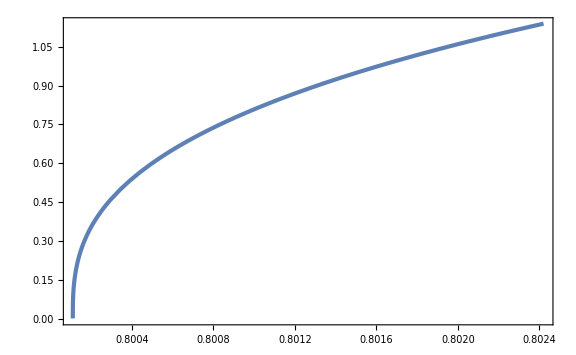

```mathematica
Plot[MoMks[mu,-3.78],{mu,muthint[-3.78],mu2int[-3.78]}]
```

```mathematica
f[z_]=1/2 z(z^2-3)(Erf[1/2 √(5/2)z]+Erf[√(5/2)z])+√(2/(5π))((8/5+31/4 z^2)Exp[-5/8 z^2]+(-8/5+1/2 z^2)Exp[-5/2 z^2]);
```

```mathematica
gineV=(1.783 10^-33)^-1;
MpcinvineV=(10^6 3.086 10^16)^-1 1.973 10^-7;
KineV=(1.16 10^4)^-1;
MplineV=2.435 10^(18+9);
kminvsinvMpcineV=(10^3 6.582 10^-16)/(3.086 10^16 10^6);
keq=0.07 0.143
```

0.01001

```mathematica
((10^20 gineV(*(3/(2π))^(3/2)*)(3 2π)^(-3/2)(1.56 10^13 MpcinvineV)^3)/(0.12 3 MplineV^2(100 kminvsinvMpcineV)^2))^-1
```

1.4281×10^-14

```mathematica
PG[x_,sg2_]=1/(√(2π sg2))Exp[-x^2/(2sg2)];
```

```mathematica
fPBH[Mks_,ks_,As_,mu_,γ_]=Mks/10^20 MoMks[mu,γ](ks/(1.56 10^13))^3(f[mu/(√As)]PG[mu,As])/(1.43 10^-14)Abs[dLogMdmu[mu,γ]]^-1 UnitStep[mu-muthint[γ]];
```

```mathematica
fPBH[10^20,1.56 10^13,10^-2,muthint[-3.78]+10^-2,-3.78]
```

43.0382

```mathematica
fPBHListγm378=Flatten[ParallelTable[{MoMks[muthint[-3.78]+10^logmu,-3.78],10^logA,fPBH[10^20,1.56 10^13,10^logA,muthint[-3.78]+10^logmu,-3.78]//Quiet},{logmu,-10,Log10[mu2int[-3.78]-muthint[-3.78]],10^-2},{logA,-4,0,10^-2}],1];//AbsoluteTiming
```

{134.834,Null}

```mathematica
Export["fPBHγm378.dat",fPBHListγm378];
```

```mathematica
fPBHListγm378=Import["fPBHγm378.dat"]//ToExpression;
```

```mathematica
fPBHintγm378[M_,A_]=Interpolation[fPBHListγm378][M,A]UnitStep[MoMks[mu2int[-3.78],-3.78]-M,M-MoMks[muthint[-3.78]+10^-10,-3.78]];
```

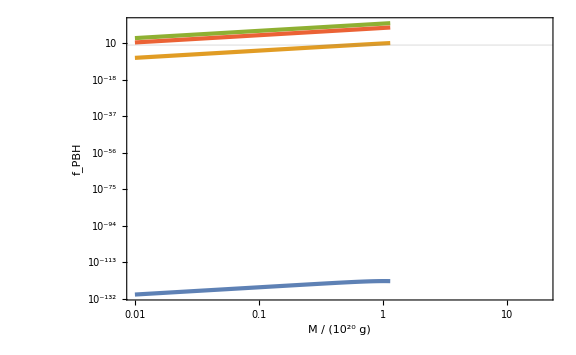

```mathematica
LogLogPlot[{fPBHintγm378[M,10^-3],fPBHintγm378[M,10^-2],fPBHintγm378[M,10^-1],fPBHintγm378[M,1]},{M,0.01,20},GridLines->{None,{1}},FrameLabel->{Row[{M," / (10^20 g)"}],Subscript[f, PBH]},PlotRange->Full]
```

```mathematica
NIntegrate[fPBHintγm378[E^logM,10^-2],{logM,Log[10^-2],Log[10]}]
```

2.99324

```mathematica
fPBHAListγm378=ParallelTable[{10^logA,NIntegrate[fPBHintγm378[E^logM,10^logA],{logM,Log[10^-2],Log[10]}]},{logA,-3,0,10^-2}];//AbsoluteTiming
```

{2.6486,Null}

```mathematica
Export["fPBHAγm378.dat",fPBHAListγm378];
```

```mathematica
fPBHAListγm378=Import["fPBHAγm378.dat"]//ToExpression;
```

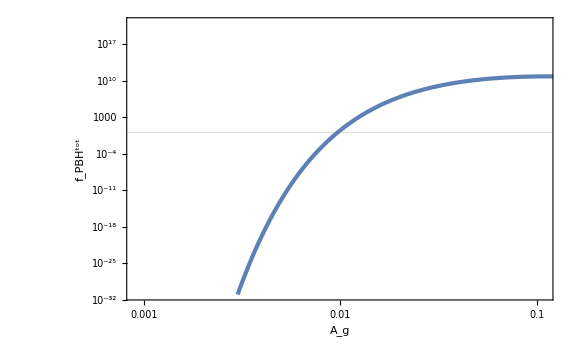

```mathematica
ListLogLogPlot[fPBHAListγm378,FrameLabel->{{Subscript[f, PBH]^tot,None},{Subscript[A, "g"],γ==-3.78}},PlotRange->{{0.9 10^-3,1.1 10^-1},{10^-31,10^21}},GridLines->{None,{1}}]
```

```mathematica
fPBHAintγm378[A_]=Interpolation[fPBHAListγm378][A];
```

```mathematica
A1γm378=A/.FindRoot[Log10[fPBHAintγm378[A]]==0,{A,0.005}]
```

0.00964987

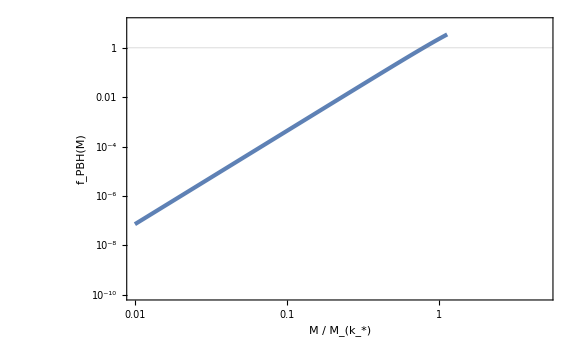

```mathematica
LogLogPlot[fPBHintγm378[M,A1γm378],{M,0.01,10},GridLines->{None,{1}},FrameLabel->{{Subscript[f, PBH][M],None},{Row[{M," / ",Subscript[M, SubStar[k]]}],γ==-3.78}},PlotRange->{{10^-2,5},{10^-10,10}}]
```